Learning the quantum algorithm for state overlap

Lukasz Cincio et al 2018 New J. Phys. 20 113022
Notebook: Óscar Amaro, June 2021 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
Demonstration of overlap for single qubit states via Bell-basis algorithm.

## Style

```mathematica
fntsz=20;
imgsz=400;
```

## Figure 9

Cos[α/2]^2

Cos[α/2]^2

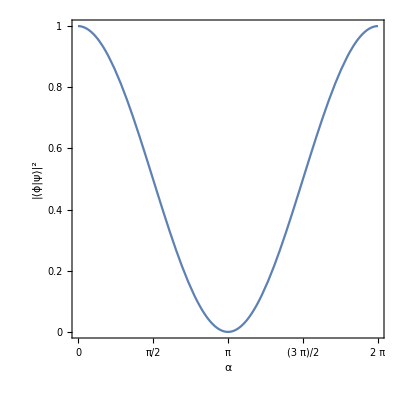

```mathematica
Clear[ψ,ϕ,ov1,ov2,α,H,P,CNOT,ρ,σ,circ,measure,c]

(* by definition *)
ψ=({1,0}+{0,1})/√2;
ϕ=({1,0}+Exp[I α]{0,1})/√2;
(* overlap *)
ov1=Refine[Abs[ψ.ϕ]^2//ComplexExpand//Simplify,{α∈Reals}]

(* by gate *)
(* gates *)
CNOT={{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}};
P={{1,0},{0,Exp[I α]}};
H=HadamardMatrix[2];
(* states *)
ψ=H.{1,0};
ϕ=P.H.{1,0};
(* initial wave function *)
psi0=ArrayFlatten[KroneckerProduct[ψ,ϕ],1];
(* full circuit *)
circ=KroneckerProduct[H,IdentityMatrix[2]].CNOT.psi0//FullSimplify;
(* measure in computational basis |<ψ|00>|^2,|<ψ|01>|^2,... *)
measure=Table[Refine[Abs[circ.IdentityMatrix[4][[1]]]^2//ComplexExpand//Simplify,α∈Reals],{i,1,4}];
(* post-processing weighting *)
c={1,1,1,-1};
(* overlap: final result *)
ov2=measure.c//Simplify

(* plot *)
Plot[ov2,{α,0,2π},Frame->True,Axes->False,FrameStyle->Directive[Black],AspectRatio->1,FrameLabel->{Style["α",Black,fntsz],Style["|⟨ϕ|ψ⟩|^2",Black,fntsz]},FrameTicksStyle->fntsz,ImageSize->imgsz,FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},None},{{0,Pi/2,Pi,3π/2,2Pi},None}}]
```